Single allele equations

```mathematica
ClearAll["Global`*"]
```

## System of equation

### Solving x (frequency) as a function of l (activity)

```mathematica
FullSimplify[DSolve[{x'[l]==b(L/l -1), x[1] == x0},x[l],l]]
```

{{x[l]→b-b l+x0+b L Log[l]}}

#### b = f’(L)/2f(L) / (Ne * v * r_0)

### Equation for minimum activity (Linf)

```mathematica
FullSimplify[l /. Solve[b(1- l+ L Log[l])== 0, l]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-L ProductLog[-ⅇ^(-1/L)/L]}

### Mean activity (L = \sum l_i x_i)

```mathematica
FullSimplify[x /. Solve[Eliminate[{x==FullSimplify[Integrate[1, {l,1, y }]/ Integrate[1/ l, {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]][[1]]
```

L

### Diversity of PRDM9 (K_e = 1 / \sum x_i^2)

```mathematica
FullSimplify[x /. Solve[Eliminate[{x==FullSimplify[Integrate[1/ l, {l,1, y }]/Integrate[b( 1-l+L Log[l])/l , {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2/(b-2 b L-b L ProductLog[-ⅇ^(-1/L)/L])

### Landscape of hotspots (V = \sum l_i x_i^2)

```mathematica
FullSimplify[x /. Solve[Eliminate[{x==FullSimplify[Integrate[b( 1-l+L Log[l]), {l,1, y }]/ Integrate[1/ l, {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1/2 b L (-1+2 L+L ProductLog[-ⅇ^(-1/L)/L])

### \sum l_i^2 x_i

```mathematica
FullSimplify[x /. Solve[Eliminate[{x==FullSimplify[Integrate[l, {l,1, y }]/ Integrate[1/ l, {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 (L-L^2 ProductLog[-ⅇ^(-1/L)/L])

## Chart and graphic for single allele equations

```mathematica
Manipulate[GraphicsRow[{Plot[{b( 1-l+L Log[l])/a , b/a(1- L+ L Log[L])},{l,0,1},GridLines->{{-L ProductLog[-ⅇ^(-1/L)/L],L},None}, PlotRange->{{0,1},{0,1}}],Module[{sol},sol=NDSolve[{x'[t]==b (l[t]-L) x[t],l'[t]==-a l[t] x[t],g'[t]==b g[t](g[t]-1- L Log[g[t]]) -a g[t]x0,x[0]==x0,l[0]==1, g[0]==1},{x,l, g},{t,0,15}];Plot[Evaluate[{x[t],b/a(1- L+ L Log[L]),l[t]}/.sol],{t,0,15},PlotRange->Full,GridLines->{None,{-L ProductLog[-ⅇ^(-1/L)/L],L}}]]}],{{b,4},0,10},{{a,1},0,10},{{L,0.5},0,1},{{x0,0.0001},0,0.001},Paneled->False]
```

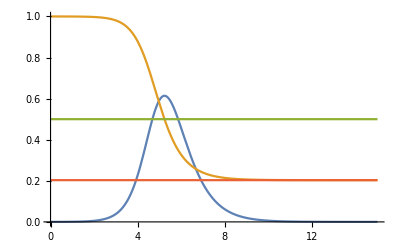

```mathematica
Module[{sol},sol=NDSolve[{x'[t]==4 (l[t]-0.5) x[t],l'[t]==- l[t] x[t],g'[t]==4 g[t](g[t]-1- 0.5 Log[g[t]]) -1 g[t]0.0001,x[0]==0.0001,l[0]==1, g[0]==1},{x,l, g},{t,0,15}];Plot[Evaluate[{x[t],l[t],0.5,-0.5 ProductLog[-ⅇ^(-1/0.5)/0.5]}/.sol],{t,0,15},PlotRange->Full]]
```

```mathematica
Export["disks.svg",%]
```

disks.svg

Approximation of f’/2f for polynomial fitness

```mathematica
F[x]= x^k/(x^k + a^k)
```

x^k/(a^k+x^k)

```mathematica
FullSimplify[D[F[x], x]/ (2F[x])]
```

(a^k k)/(2 a^k x+2 x^(1+k))